1/(4 √x)ⅇ^(-x^2/4) (π x^2 BesselI[-1/4,x^2/4]+π (2+x^2) BesselI[1/4,x^2/4]+π x^2 BesselI[3/4,x^2/4]+π x^2 BesselI[5/4,x^2/4]+2 ⅈ 2^(3/4) ⅇ^(x^2/4) √x Gamma[3/4] Hypergeometric1F1[-1/4,1/2,-x^2/2]-4 ⅈ 2^(1/4) ⅇ^(x^2/4) x^(3/2) Gamma[5/4] Hypergeometric1F1[1/4,3/2,-x^2/2])

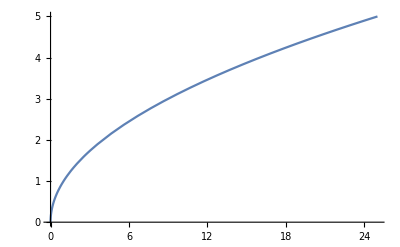

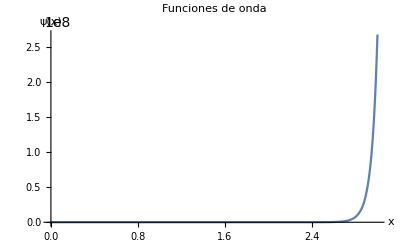

```mathematica
a=1/2;
M2[y_,a_]:= Exp[-y^2*(1-a)];
M1[y_,a_]:=(3-Cos[2*(1-a)*y])/4;
M[x_,a_]:=x^(1-a);
M3[x_,a_]=Convolve[M2[y,a],M[y,a],y,x]

Plot[M[x,a],{x,-25,25},PlotRange->All]

λ1=x/2*(D[M[x,a],x]/M[x,a]+Sqrt[-8*1*M[x,a]^4+4*x^2M[x,a]^5+D[M[x,a],x]^2]/M[x,a]);
λ2=x/2*(D[M[x,a],x]/M[x,a]-Sqrt[-8*1*M[x,a]^4+4*x^2M[x,a]^5+D[M[x,a],x]^2]/M[x,a]);
ψ=Exp[λ1]+Exp[λ2];
Plot[ψ,{x,-3,3},PlotRange->All,PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```